# NG_4 T_01 ШпакАндрей. Многослойный персептрон

Искусственная нейросеть и логические операции. Реализуйте три разных нейросети небольшого размера, архитектуры которых приведены на Рис.1. В качестве функции активации используйте пороговую функцию UnitSteppaclet:ref/UnitStep. Математическая модель нейрона (нейросети kmANN21) описывается формулой (DisplayFormulaNumbered).

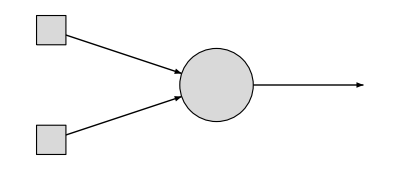
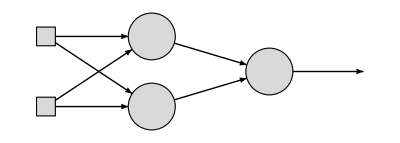
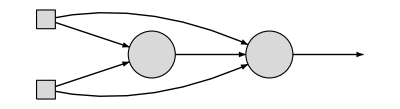
-Graphics-kmANN21 | -Graphics-kmANN221 | -Graphics-kmANN211
Рис 1. Искусственные нейросети

kmANN21_(W⃗)(x⃗):=UnitStep(w_1 x_1+w_2 x_2+w_0)

Решение:

-Graphics-

```mathematica
ClearAll[kmANN21,kmANN221,kmANN211];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
kmANN[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{(x1*W11[[1]]).(x2*W12[[1]]),(x1*W11[[2]]).(x2*W12[[2]])}];
```

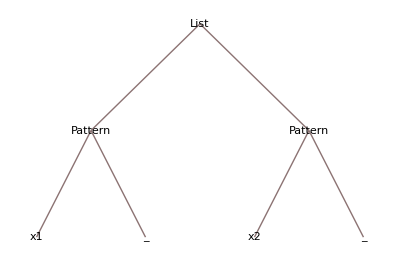

```mathematica
{x1_,x2_}//TreeForm
```

```mathematica
Prefix[f@{z1, z2}]
```

f@{z1,z2}

```mathematica
{1, 2, 3}*{4,5,6}
```

{4,10,18}

```mathematica
Plus@@({1, 2, 3}*{4,5,6})
```

32

```mathematica
{1, 2, 3}.{4,5,6}
```

32

```mathematica
W11={w1,w2}
x1*W11
```

{w1,w2}

{w1 x1,w2 x1}

```mathematica
x1.W11
```

x1.{w1,w2}

```mathematica
const=1
const.{w1,w2}
const.{1,2}
{const, const}.{w1,w2}
```

1

1.{w1,w2}

1.{1,2}

w1+w2

```mathematica
W12={w3,w4}
x1*W11
x2*W12
```

{w3,w4}

{w1 x1,w2 x1}

{w3 x2,w4 x2}

```mathematica
x1*W11[[1]]
x2*W12[[1]]
```

w1 x1

w3 x2

```mathematica
x1*W11[[2]]
x2*W12[[2]]
```

w2 x1

w4 x2

```mathematica
(x1*W11[[1]]).(x2*W12[[1]])
```

(w1 x1).(w3 x2)

```mathematica
(x1*W11[[2]]).(x2*W12[[2]])
```

(w2 x1).(w4 x2)

```mathematica
W2.{(x1*W11[[1]]).(x2*W12[[1]]),(x1*W11[[2]]).(x2*W12[[2]])}
```

W2.{(w1 x1).(w3 x2),(w2 x1).(w4 x2)}